## Load Lib

```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["HappyTile.wl"]
Get["HappyCluster.wl"]
```

ChooseColor::shdw: Symbol ChooseColor appears in multiple contexts {HappyCluster`,DepictTile`}; definitions in context HappyCluster` may shadow or be shadowed by other definitions.

ChoosePoints::shdw: Symbol ChoosePoints appears in multiple contexts {HappyCluster`,HappyTile`}; definitions in context HappyCluster` may shadow or be shadowed by other definitions.

# First Phase

This Phase is to use Points representing angle and intersection test to generate and filter cases.

### Tiles Polygons

```mathematica
H2poly=;
H1poly=;
```

```mathematica
H8poly=Polygon[];
H7poly=Polygon[];
```

```mathematica
AH7superPoly=;
H8superPoly=;
```

```mathematica
metaTile[pos_,dir_:0,pt_,choice_:True]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
cluster[pos_,dir_:0,pt_,choice_:False]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
clusterSuper1[pos_,dir_:0,pt_,choice_:False]:=With[{
vertices=If[
TrueQ[choice],
RotationMatrix[dir*Pi/6].#&/@,
RotationMatrix[dir*Pi/6].#&/@
]
},
Polygon[vertices+Threaded[pos-vertices[[pt]]]]
]
```

```mathematica
angleVertices[angle_][poly_]:=First/@Position[PolygonAngle[poly],_?(#==2Pi*angle&),{1}]
```

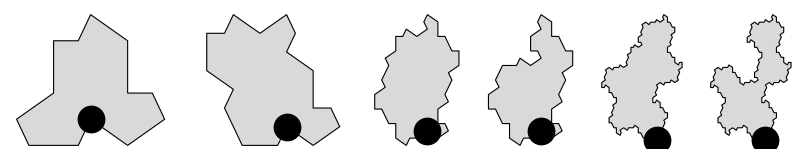

```mathematica
Graphics[
{
LightGray,
EdgeForm[Black],
#,
Black,PointSize[.05],
Point[First[#][[1]]]
}
]&/@{H1poly,H2poly,H8poly,H7poly,H8superPoly,AH7superPoly}//GraphicsRow[#,ImageSize->800]&
```

```mathematica
angleToPointsBuildFunction=Function[
{choice,tileFunction},
angleToPoints[ToString[tileFunction]][choice]=Association[#->Join@@Position[
RegionMember[
tileFunction[{0,0},0,1,choice],
CirclePoints[First[tileFunction[{0,0},0,1,choice]][[#]],{1/4,Pi/12},12]
],True
]&/@Range[Length[First[tileFunction[{0,0},0,1,choice]]]]]
];
```

### Project Tiles Code

```mathematica
metaTileCode[pos_,dir_:0,pt_,False]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@
]
```

```mathematica
metaTileCode[pos_,dir_:0,pt_,True]:=With[{
vertices=
},
{pos+RotationMatrix[dir*Pi/6].(#1-vertices[[pt]]),Mod[#2+If[TrueQ[#3],-dir,dir],12],#3,#4}&@@@{{{0,0},0,False,1}}
]
```

```mathematica
clusterCode[pos_,dir_,pt_,False]:=With[
{H7vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H7vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

```mathematica
clusterCode[pos_,dir_,pt_,True]:=With[
{H8vertices=},
	{
		pos+RotationMatrix[dir Pi/6].(#1-H8vertices[[pt]]),
		Mod[If[TrueQ[#3],-dir,dir]+#2,12],
		#3,#4
	}&@@@
];
```

### angle information

```mathematica
angleToPoints["metaTile"][True]=;
angleToPoints["metaTile"][False]=;
```

```mathematica
angleToPoints["cluster"][True]=;
angleToPoints["cluster"][False]=;
```

```mathematica
angleToPoints["clusterSuper1"][True]=;
angleToPoints["clusterSuper1"][False]=;
```

```mathematica
getPointsOccupation[tileFunction_][dir_,pt_,choice_]:=Mod[#+dir,12,1]&/@(pt/.angleToPoints[ToString[tileFunction]][choice])
```

### intersectingQ

```mathematica
intersectingQ[p1_Polygon,p2_Polygon,dimension_Integer:10]:=With[{res=PlanarPolygonFragmentation[p1,p2,dimension]},If[res==={}||Total[Length/@res]==3,False,True]]
intersectingQ[ps_List,dimension_Integer:10]:=Fold[
If[
#1===True,
True,
With[{res=PlanarPolygonFragmentation[#1,#2,dimension]},
If[Total[Length/@res]==3,SortBy[res,Length][[1,1]],True]
]
]&,
ps
]
```

### all rotations

```mathematica
allRotations=Function[r,Sort[Apply[{Mod[#1+r,12],#2,#3}&,#,{1}]]]/@Range[0,11]&;
```

### 1/3 v.f for 0-super-tile

```mathematica
oneThirdVF=;
```

### 0-super-tile

Brad’s clever way:

```mathematica
vertexClass[True]=Association[
MapIndexed[
First[#2]->Lookup[(Merge[Association[MapIndexed[#1->#2&,hatVertices@@#]]&/@,Join@@#&]),Key[#1]]&,
First[cluster[{0,0},10,1,True]]
]
];
vertexClass[False]=Association[
MapIndexed[
First[#2]->Lookup[(Merge[Association[MapIndexed[#1->#2&,hatVertices@@#]]&/@,Join@@#&]),Key[#1]]&,
First[cluster[{0,0},10,1,False]]
]
];
```

All vertex configuration from hat tile:

```mathematica
validVF=Union@@(#[{1,Sqrt[3]}][[All,All,3]]&/@{oneThirdAndTwoThirdTheoremList,oneThirdVertexTheoremLis})
```

{{8,4},{8,12},{8,14},{10,2},{10,6},{2,2,2},{2,2,6},{2,6,6},{4,4,4},{4,4,12},{4,12,12},{4,12,14},{12,12,14}}

```mathematica
allOneThirdStatesForOne=Join@@(Tuples[{Range[0,11],oneThirdClusterVertex[#],{#}}]&/@{True,False});
allTwoThirdStatesForOne=Join@@(Tuples[{Range[0,11],twoThirdClusterVertex[#],{#}}]&/@{True,False});
allOneThirdStatesForOne//Length
allTwoThirdStatesForOne//Length
```

312

204

### Classify cases:

```mathematica
classifiedByVertexAndPoints=GroupBy[
Join[allOneThirdStatesForOne,allTwoThirdStatesForOne],
{Sort[getPointsOccupation[cluster]@@#]&,Sort[#[[2]]/.Join[vertexClass[#[[3]]],vertexClass[#[[3]]]]]&}
];
```

```mathematica
cases=Join@@Apply[
Tuples[{
Lookup[Lookup[classifiedByVertexAndPoints,Key[{1,2,3,4,5,6,7,8}],{}],Key[Sort[#2]],{}],
Lookup[Lookup[classifiedByVertexAndPoints,Key[{9,10,11,12}],{}],Key[Sort[#1]],{}]
}]&,
{{#1},{##2}}&@@@(Join@@(Permutations/@validVF)),
{1}
];
cases//Length
```

375

```mathematica
cases=DeleteDuplicatesBy[Sort][cases];
cases//Length
```

233

### Points to Cases

```mathematica
pointsToCases=GroupBy[Join[allOneThirdStatesForOne,allTwoThirdStatesForOne],Sort[getPointsOccupation[cluster]@@#]&];
```

```mathematica
cases=Tuples[
{
pointsToCases[{2,3,4,5}],
pointsToCases[{1,6,7,8,9,10,11,12}]
}
];
cases//Length
```

442

### Intersection Test

```mathematica
Timing[res3=Select[
cases,
intersectingQ[cluster[{0,0},##]&@@@#,15]=!=True&
];]
```

{10.2813,Null}

```mathematica
res3//Length
```

186

Use 1/3 v.f. to test validity:

```mathematica
Iconize[res3]
```

Then, we use intersection test to see if there is any impossible vertex, we need a generator and an intersection filter. Generator generates all possible cases according to what we have, all candidate vertex configurations, and filter with intersection. That is the part 2 job:

# Second Phase

## Vertex Number Convention

First vertex position shown as black vertex, and continue to number counter-clockwise.

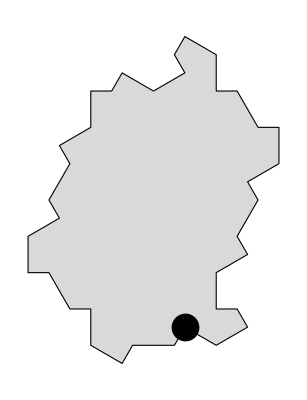
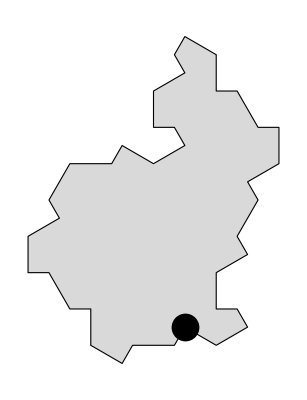

```mathematica
Graphics[
{
LightGray,
EdgeForm[Black],
#,
Black,PointSize[.05],
Point[First[#][[1]]]
}
]&/@{Polygon[],Polygon[]}
```

Notice: every hat tile are numbered as 14 vertices rule, which means each edge with length 2 is made up with two edges with length 1 and a 1/2 vertex.

## First Phase result

```mathematica
resultofFirstPhase=;
```

## Reduce 3*(1/3) and 1/3+2/3 v.f of H8

### Use hat tile vertex configuration (eliminate 5 cases including {6,6,6})

Cluster codes:

```mathematica
allClusterCodes=Map[Prepend[#,{0,0}]&,resultofFirstPhase,{2}];
```

Test if it satisfy hat tiling v.f.:

```mathematica
hatCodeValidQ[clustercode_]:=Block[{
hatCode=Apply[codeJoin,Apply[clusterCode,clustercode,{1}],{0}],
vertexConfiguration,
allValidVFs=DeleteDuplicates[Sort/@(Join@@(#[{1,Sqrt[3]}][[All,All,3]]&/@{
oneThirdAndTwoThirdTheoremList,
oneThirdVertexTheoremLis,
oneHalfTheoremList,
TshapeList,
oneFourthAndThreeFourthTheoremList,
oneFourthVertexTheoremLis
}))]
},
vertexConfiguration=Sort/@Select[getVerticesInf[hatCode][[All,All,1]],(Total[(#/.vertexAngles)]==1&)];
vertexConfiguration=Select[
vertexConfiguration,
Function[testvf,
!Or@@(MatchQ[#,Sort[testvf]]&/@allValidVFs)
]
];
If[
Length[vertexConfiguration]>0,
vertexConfiguration,
True
]
]
```

Delete all invalid hat v.f. cases:

```mathematica
invalidCases=Cases[
allClusterCodes,
code_/;hatCodeValidQ[code]=!=True:>({code,hatCodeValidQ[code]})
];
```

```mathematica
Show[{
show[clusterCode@@@#1,ChooseColor->{LightBlue}],
Graphics[{EdgeForm[Black],Red,Disk[Keys[#2],0.3]}]
}]&@@@invalidCases//List//Grid
```

-Graphics-

Test if they satisfy H7/H8 cluster 1/3 v.f.

```mathematica
res1=DeleteCases[allClusterCodes,Alternatives@@invalidCases[[All,1]]];
```

```mathematica
Iconize[res1[[All,All,2;;]]]
```

### Using grow function (eliminate a bunch)

At last, there is a introduction about how this grow function works.

There are two important list for grow function to generate cases, one is 3*(1/3) theorem list, the other is 1/3+2/3.

Here we use 3*(1/3) theorem list with 24 elements at first, which has been derived before. 1/3+2/3 is the same as above res1.

```mathematica
(*{{0,#1[[2]],#1[[3]]},{Mod[#2[[1]]-#1[[1]],12],#2[[2]],#2[[3]]},{Mod[#3[[1]]-#1[[1]],12],#3[[2]],#3[[3]]}}&@@@//Iconize*)
```

```mathematica
(*{{0,#1[[2]],#1[[3]]},{Mod[#2[[1]]-#1[[1]],12],#2[[2]],#2[[3]]}}&@@@//Iconize*)
```

```mathematica
oneThirdTheoremListCluster=;
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

A little slow test dead points function

```mathematica
getDeadPoints[code_]:=Block[{
poly=PolygonListUnion[cluster@@@code],
pointsBranches = generatorH8[
		Select[clusterTilingState[code]["boundaryPoints"]
			,Total[Lookup[clusterVertexAngles[Last[#2]], #1, {}]& @@@ #] <1 &]
	]
},
Cases[
KeyValueMap[
Function[{pt,newcodes},
pt->(If[intersectingQ[Prepend[cluster@@@#,poly],20]===True,Nothing,#]&/@newcodes)],
pointsBranches
],
pt_/;Length[pt[[2]]]==0:>First[pt],
{1}
]
]
```

### 1/3: 69 to 15 (372s)

There are less 1/3 v.f, maybe we should eliminate them first:

```mathematica
reduceProcessList=FixedPointList[
Function[list,
initcodes=Map[Prepend[#,{0,0}]&,list,{2}];
g=Map[#1->Last[Reap[growH8Tiling[clusterTilingState[#1],branchNumLimit->Infinity]]]&,initcodes];
invalidCases=Select[g,#[[2]]=!={}&];
oneThirdTheoremListCluster=DeleteCases[oneThirdTheoremListCluster,Alternatives@@invalidCases[[All,1,All,2;;]]]
],
oneThirdTheoremListCluster,
10
];//Timing
```

{335.938,Null}

```mathematica
Length/@reduceProcessList
```

{69,17,15,15}

```mathematica
Iconize[oneThirdTheoremListCluster]
```

```mathematica
oneThirdTheoremListCluster=;
```

### 1/3+2/3: 186 to 69 (600s)

Do the same thing to the 1/3+2/3, it feels like machine learning?

```mathematica
reduceProcessList2=FixedPointList[
Function[list,
initcodes=Map[Prepend[#,{0,0}]&,list,{2}];
g=Map[#1->Last[Reap[growH8Tiling[clusterTilingState[#1],branchNumLimit->Infinity]]]&,initcodes];
invalidCases=Select[g,#[[2]]=!={}&];
oneThirdAndTwoThirdTheoremListCluster=DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@invalidCases[[All,1,All,2;;]]]
],
oneThirdAndTwoThirdTheoremListCluster,
10
];//Timing
```

{595.656,Null}

```mathematica
Length/@reduceProcessList2
```

{186,93,66,66}

```mathematica
oneThirdAndTwoThirdTheoremListCluster//Iconize
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

### 1/3: 15 to 14 (346s) (42s)

There are less 1/3 v.f, maybe we should eliminate them first:

```mathematica
reduceProcessList3=FixedPointList[
Function[list,
initcodes=Map[Prepend[#,{0,0}]&,list,{2}];
g=Map[#1->Last[Reap[growH8Tiling[clusterTilingState[#1],branchNumLimit->Infinity]]]&,initcodes];
invalidCases=Select[g,#[[2]]=!={}&];
oneThirdTheoremListCluster=DeleteCases[oneThirdTheoremListCluster,Alternatives@@invalidCases[[All,1,All,2;;]]]
],
oneThirdTheoremListCluster,
10
];//Timing
```

impossible Vertices:{{6,-4 √3},{5,-5 √3}}

{40.0156,Null}

```mathematica
Length/@reduceProcessList3
```

{15,14,14}

```mathematica
Iconize[oneThirdTheoremListCluster]
```

```mathematica
oneThirdTheoremListCluster=;
```

### 1/3+2/3: 66 to 66 - fixed

```mathematica
reduceProcessList4=FixedPointList[
Function[list,
initcodes=Map[Prepend[#,{0,0}]&,list,{2}];
g=Map[#1->Last[Reap[growH8Tiling[clusterTilingState[#1],branchNumLimit->Infinity]]]&,initcodes];
invalidCases=Select[g,#[[2]]=!={}&];
oneThirdAndTwoThirdTheoremListCluster=DeleteCases[oneThirdAndTwoThirdTheoremListCluster,Alternatives@@invalidCases[[All,1,All,2;;]]]
],
oneThirdAndTwoThirdTheoremListCluster,
10
];//Timing
```

{71.875,Null}

Nothing changed any more.

```mathematica
Length/@reduceProcessList4
```

{66,66}

### Record Result

14 1/3 + 66 1/3+2/3

#### Iconize

```mathematica
Iconize/@{oneThirdTheoremListCluster,oneThirdAndTwoThirdTheoremListCluster}
```

{,}

```mathematica
oneThirdTheoremListCluster=;
```

```mathematica
oneThirdAndTwoThirdTheoremListCluster=;
```

Visualize them:

#### 1/3 (14 cases)

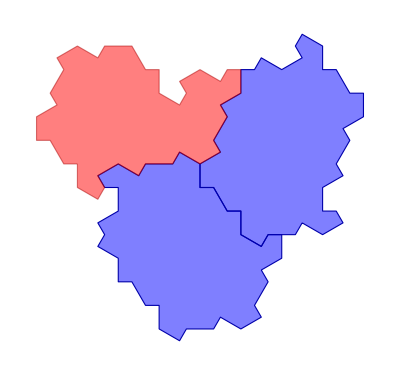
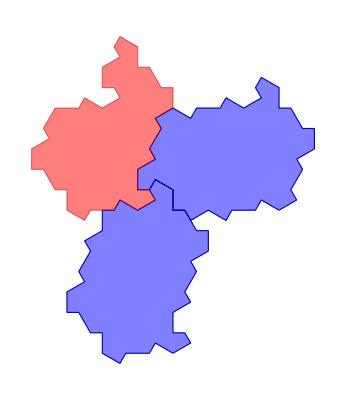
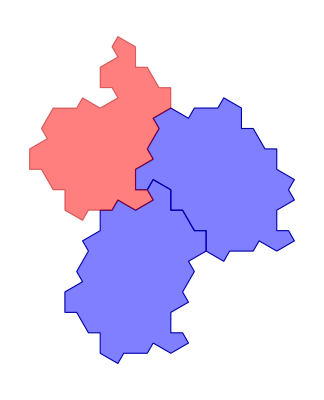
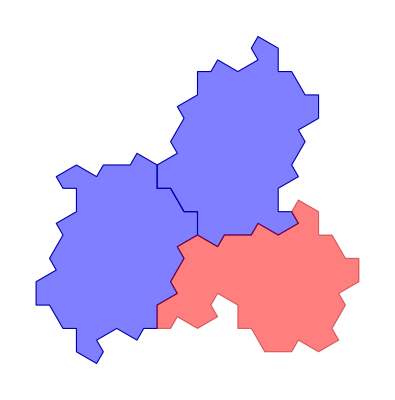
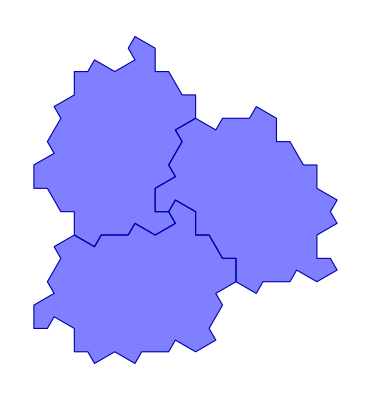
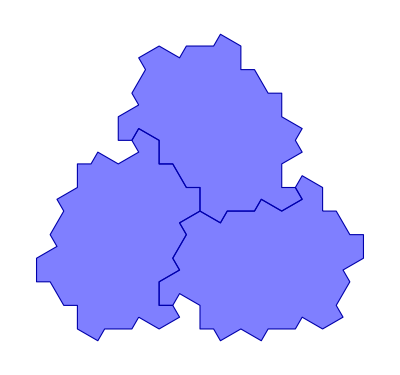
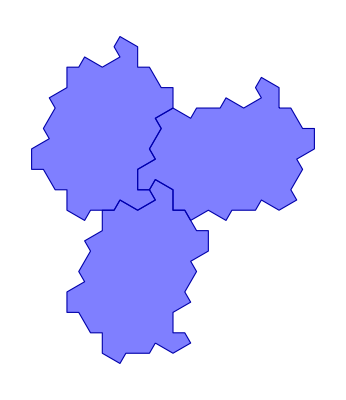
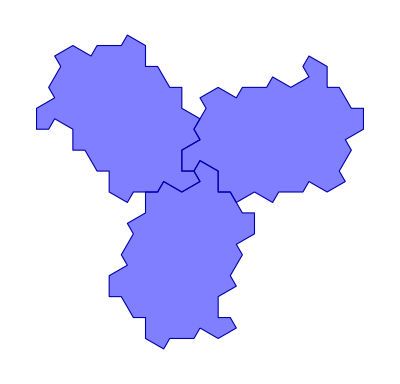
-Graphics-32 | True
12 | False
12 | True | -Graphics-20 | True
20 | True
4 | False | -Graphics-20 | True
4 | True
4 | False | -Graphics-38 | True
32 | True
12 | False | -Graphics-4 | True
4 | True
4 | True | -Graphics-12 | True
12 | True
12 | True | -Graphics-20 | True
20 | True
4 | True
-Graphics-20 | True
20 | True
20 | True | -Graphics-20 | True
4 | True
4 | True | -Graphics-32 | True
32 | True
32 | True | -Graphics-32 | True
12 | True
12 | True | -Graphics-32 | True
12 | True
32 | True | -Graphics-38 | True
32 | True
12 | True | -Graphics-38 | True
32 | True
32 | True

```mathematica
Labeled[
visualize[#,ChooseColor->{Blue,Red}],
Grid@#[[All,3;;4]]]&/@SortBy[#[[All,-1]]&][Map[Prepend[#,{0,0}]&,oneThirdTheoremListCluster,{2}]]//Partition[#,UpTo[7]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

#### 1/3+2/3 (66 cases)

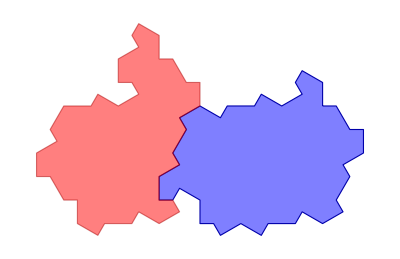
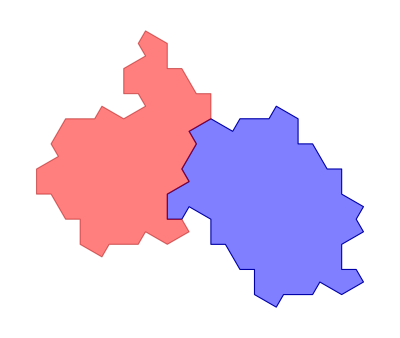
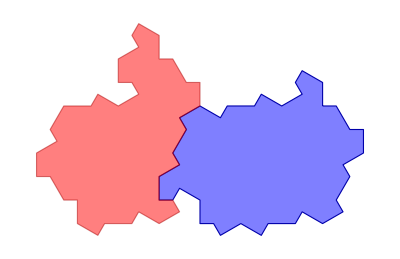
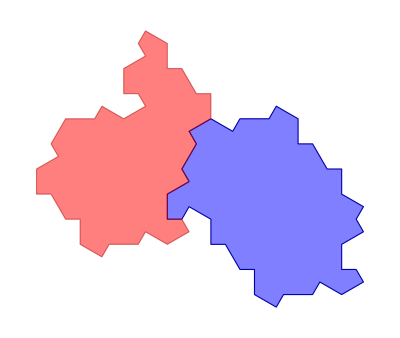
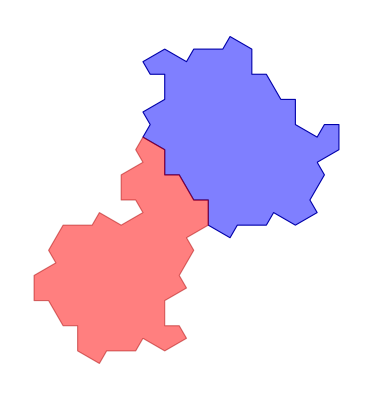
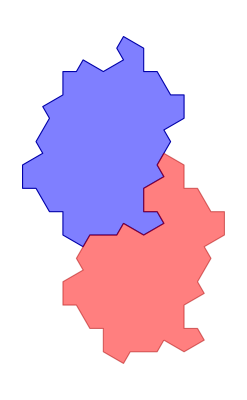
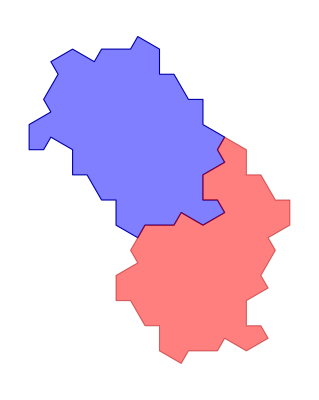
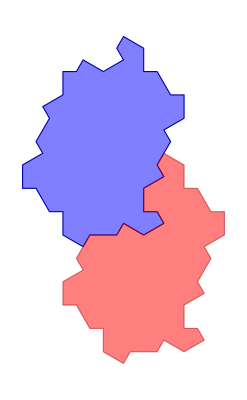
-Graphics-6 | False
18 | True | -Graphics-6 | False
2 | True | -Graphics-8 | False
16 | True | -Graphics-8 | False
42 | True | -Graphics-14 | False
30 | True | -Graphics-24 | False
4 | True | -Graphics-24 | False
20 | True | -Graphics-26 | False
2 | True | -Graphics-26 | False
18 | True | -Graphics-28 | False
42 | True | -Graphics-28 | False
16 | True
-Graphics-36 | False
20 | True | -Graphics-42 | False
20 | True | -Graphics-6 | True
22 | False | -Graphics-8 | True
20 | False | -Graphics-14 | True
30 | False | -Graphics-14 | True
10 | False | -Graphics-22 | True
2 | False | -Graphics-22 | True
40 | False | -Graphics-22 | True
34 | False | -Graphics-24 | True
44 | False | -Graphics-24 | True
38 | False
-Graphics-24 | True
20 | False | -Graphics-24 | True
32 | False | -Graphics-26 | True
18 | False | -Graphics-28 | True
16 | False | -Graphics-40 | True
30 | False | -Graphics-40 | True
10 | False | -Graphics-6 | True
32 | True | -Graphics-6 | True
18 | True | -Graphics-6 | True
12 | True | -Graphics-6 | True
2 | True | -Graphics-6 | True
38 | True
-Graphics-8 | True
30 | True | -Graphics-8 | True
16 | True | -Graphics-8 | True
10 | True | -Graphics-8 | True
42 | True | -Graphics-8 | True
36 | True | -Graphics-14 | True
20 | True | -Graphics-14 | True
30 | True | -Graphics-14 | True
4 | True | -Graphics-14 | True
10 | True | -Graphics-22 | True
2 | True | -Graphics-22 | True
38 | True
-Graphics-22 | True
18 | True | -Graphics-22 | True
12 | True | -Graphics-24 | True
42 | True | -Graphics-24 | True
36 | True | -Graphics-24 | True
16 | True | -Graphics-24 | True
10 | True | -Graphics-26 | True
12 | True | -Graphics-26 | True
2 | True | -Graphics-26 | True
38 | True | -Graphics-26 | True
18 | True | -Graphics-28 | True
10 | True
-Graphics-28 | True
42 | True | -Graphics-28 | True
36 | True | -Graphics-28 | True
16 | True | -Graphics-34 | True
4 | True | -Graphics-34 | True
10 | True | -Graphics-34 | True
36 | True | -Graphics-34 | True
30 | True | -Graphics-40 | True
4 | True | -Graphics-40 | True
10 | True | -Graphics-40 | True
20 | True | -Graphics-40 | True
30 | True

```mathematica
Labeled[
visualize[#,ChooseColor->{Blue,Red}],
Grid@#[[All,3;;4]]]&/@SortBy[#[[All,-1]]&][Map[Prepend[#,{0,0}]&,oneThirdAndTwoThirdTheoremListCluster,{2}]]//Partition[#,UpTo[11]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

## Build Cluster-Hat Pre-image

Here I tried to build pre-image graph with 5 1/3 key points, some of them will cause non-connected graph, which is not handled yet.

So, the following are for reference now:

```mathematica
Get["toptile.wl"]
```

```mathematica
codes=Map[Prepend[#,{0,0}]&,Join[oneThirdAndTwoThirdTheoremListCluster,oneThirdTheoremListCluster],{2}];
```

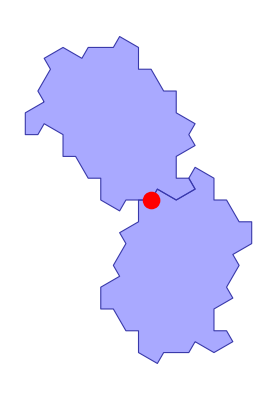
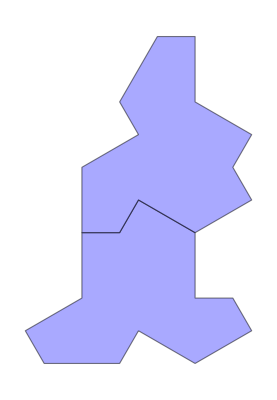
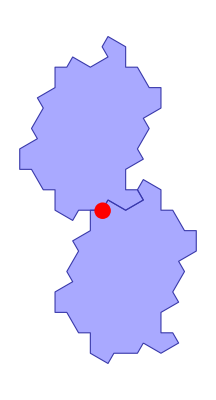
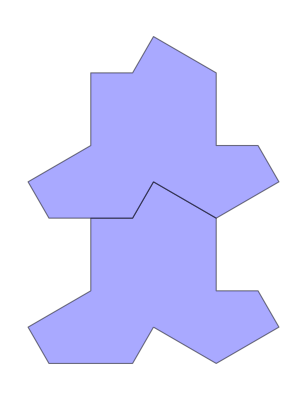
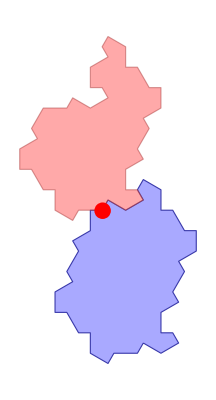
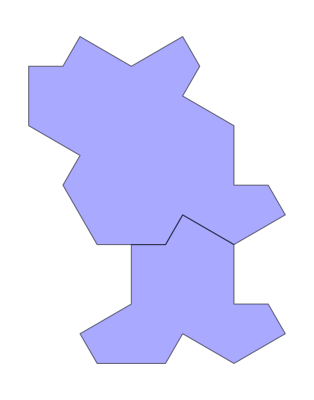
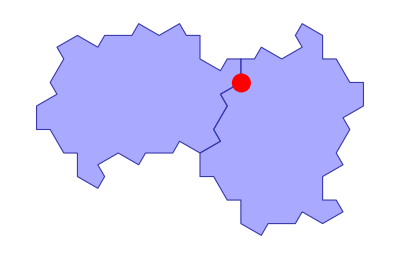
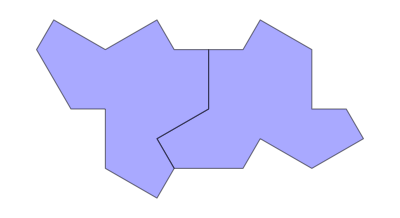
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- |  |  |

```mathematica
Function[code,Block[{graph,reBuiltCodes},
graph=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@code];
reBuiltCodes=buildClusterCodes[h2Tile,h1Tile][graph];
If[
FreeQ[reBuiltCodes,Missing],
Row[{
Show[#,Graphics[{Red,Disk[{0,0},.7]}]]&@visualize[code],
Graphics[{Lighter@Blue,Opacity[.5],EdgeForm[Black],(metaTile[#1,#2,2,#4]&@@@reBuiltCodes)}]
},Style["↔",40,Gray]
],
Nothing
]
]]/@codes//Partition[#,UpTo[4]]&//Grid[#,FrameStyle->LightGray,Frame->All]&
```

Some of cases have the same hat tile pre-image and actually, fit together the same way for H7/H8 cluster. There they are different because the original point is different, where they meet for code.